```mathematica
Julia=Compile[{x,y, cx, cy, max},
Module [ {c=cx+I*cy, z , ct=0},
z=x+I*y;
While [ Abs[z] < 2.0 && ct <= max,
z = z^2 + c;
++ct 
] ;
-ct
 ]
];
```

```mathematica
DensityPlot[Julia[x, y,0.3,0.008,200 ],
	{x, -1.5, 1.5}, {y, -1.5, 1.5},
PlotPoints -> 75, 
Mesh -> False ,
ColorFunction -> Function[x,Hue[0.05 + 0.6*x]],
ImageSize -> 500
] //Timing
```

{0.92464,-Graphics-}

```mathematica
Julia2=Compile[{x,y, cx, cy, max},
Module [ {c=cx+I*cy, z , ct=0},
z=x+I*y;
While [ Abs[z] < 2.0 && ct <= max,
z = Sin[z^2] + c;
++ct 
] ;
-ct
 ]
];
```

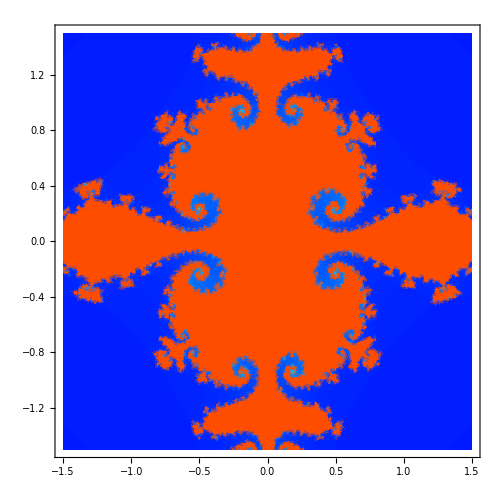
{0.984883,-Graphics-}

```mathematica
DensityPlot[Julia2[x, y,0.3,0.001,200 ],
	{x, -1.5, 1.5}, {y, -1.5, 1.5},
PlotPoints -> 75, 
Mesh -> False ,
ColorFunction -> Function[x,Hue[0.05 + 0.6*x]],
ImageSize -> 500
] //Timing
```